```mathematica
Exit[]
```

## init

```mathematica
Get["/data/mapk/mapkp4.mx"];
Get["/home/abergman/dicty/SPSA.m"]
```

```mathematica
LaunchKernels[]
ParallelEvaluate[$KernelID]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
lenX=Range[0.01,1.05,0.05]
lenX=Clip[lenX]
Length[lenX]
```

{0.01,0.06,0.11,0.16,0.21,0.26,0.31,0.36,0.41,0.46,0.51,0.56,0.61,0.66,0.71,0.76,0.81,0.86,0.91,0.96,1.01}

{0.01,0.06,0.11,0.16,0.21,0.26,0.31,0.36,0.41,0.46,0.51,0.56,0.61,0.66,0.71,0.76,0.81,0.86,0.91,0.96,1.}

21

```mathematica
{v,θ0}={{p4a, p4b, p4c, p4d, p2, p3a, p3b, p3c, p3d, p5, StotNative, StotOE, maxdose, dX}, {0.1, 0.05, 0.05, 10, 1., 0.03, 1., 70., 0.03, 1., 1., 9., 0.01, 0.0001}};
inputθ0[]:=TableForm[Table[With[{i=i},InputField[Dynamic[θ0[[i]]],Number,FieldSize->{11,1}]],{i,1,Length[θ0]}],TableHeadings->{v,{"θ0"}}]
```

```mathematica
tend=10000;
slevel:={StotNative,StotOE}
pθ0:=Thread[Rule[v,θ0]]
```

```mathematica
p4sigmoid=Function[s,p4[s]->(p4b-p4d)/(1+Exp[(p4a-(Stot-Scyto[s][t]-Smem[s][t]))/p4c])+p4d]/@{0,1};p3sigmoid=Function[s,p3[s]->(p3b-p3d)/(1+Exp[(Smem[s][t]-p3a)p3c])+p3d]/@{0,1};
```

```mathematica
myrunsim[pp___]:=With[{p=Flatten[{pp}]},
DistributeDefinitions[θ0];
Transpose@ParallelTable[
plist=Join[p,{λ->l,δ[x_]->maxdose(l+dX*x),Stot->s,p1[x_]->p5*δ[x],p3sigmoid,p4sigmoid}/.p/.pθ0,pθ0];
runsim[plist]
,{l,lenX},{s,slevel/.pθ0},Method->"FinestGrained"]
]
```

```mathematica
DistributeDefinitions["Global`*"]
$DistributedContexts=None;
```

{Global`}

## Plots

### Scaffold dose response

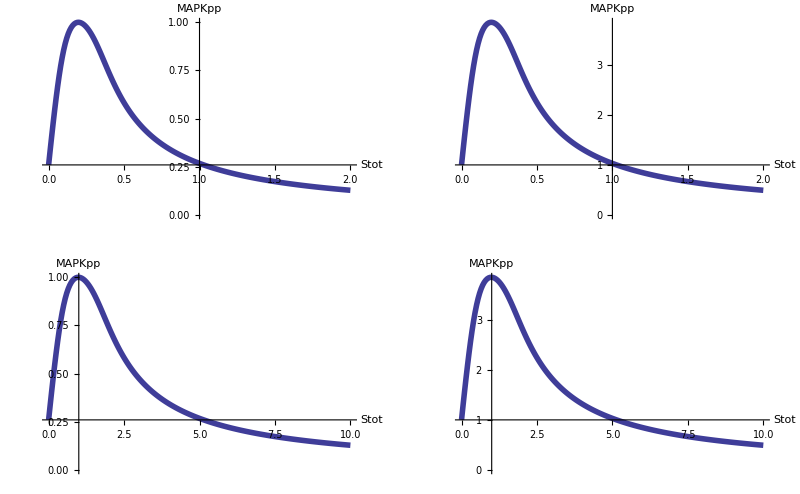

```mathematica
Block[{dat},
dat=ParallelTable[{s,MAPKpp[0]}/.runsim[p4[_]->0,p2->0,Stot->s,p1[_]->100],{s,0.0,2.0,0.01}];
Table[
ListLinePlot[dat/.{s_,m_}->{s/ss,m/ff},AxesOrigin->{1,dat[[1,-1]]/ff},AxesLabel->{"Stot","MAPKpp"},PlotStyle->Thickness[0.01],BaseStyle->{FontSize->14}],{ss,{1,0.2}},{ff,{MAXMAPKPP,dat[[1,-1]]}}]//GraphicsGrid[#,ImageSize->Full]&
]
```

### figs func

```mathematica
Off[Power::infy]
Off[Infinity::indet]
figs=Function[dat,GraphicsGrid[{{
ListLogPlot[{runsim$maxiter,dd}/.dat,PlotLabel->"tol"],
Plot[p3[0]/.p3sigmoid/.Smem[0][t]->Smem//.dat[[1,1]],{Smem,0,Max[Smem[0]/.dat]},PlotRange->{p3b/.dat[[1,1]],0},AxesLabel->{"Smem","p3[Smem]"}],
Plot[p4[0]/.p4sigmoid/.-Stot+Scyto[0][t]+Smem[0][t]->-Sves//.dat[[1,1]],{Sves,0,Max[Stot-Smem[0]-Scyto[0]/.dat]},PlotRange->{0,Max[{p4b,p4d}//.pθ0]},AxesLabel->{"Sves","p4[Sves]"}]
},
{
ListLinePlot[{λ,Scyto[0]}/.dat,PlotLabel->"Scyto"],
ListLinePlot[{λ,Smem[0]}/.dat,PlotLabel->"Smem"],
ListLinePlot[{λ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"]
},{
ListPlot[{(Stot-Smem[0]-Scyto[0]),MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp vs Sves",Joined->True,Mesh->Full,PlotStyle->{{Dotted,Thickness[0.01]},Thick},PlotRange->{0,1},AxesLabel->{"Sves","MAPKpp"}]
,
ListLinePlot[{λ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp",PlotRange->{0,1}],
ListLinePlot[{λ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat/.ComplexInfinity->0,PlotRange->{-4,4},PlotLabel->"MI"]
}},ImageSize->Full]];
```

### Uniform stim, no vesicle transport inhibition, recycling inhibition

```mathematica
Dynamic[
dat1=myrunsim[dX->0,p3d->p3b,p4b->p4d];
dat2=myrunsim[dX->0,p3d->p3b,p4d->p4b];
dat3=myrunsim[dX->0,p3d->p3b];
GraphicsColumn[figs/@{dat1,dat2,dat3},ImageSize->Full]
,TrackedSymbols:>{θ0}
]
```

### Uniform stim, vesicle transport inhibition, no recycling inhibition

```mathematica
Dynamic[
dat={
myrunsim[dX->0,p4b->p4d],
myrunsim[dX->0,p4d->p4b]};
GraphicsColumn[figs/@dat,ImageSize->Full]
,TrackedSymbols:>{θ0}
]
```

### Uniform stim, vesicle transport inhibition, with recycling inhibition

```mathematica
Dynamic[
dat=myrunsim[dX->0];
figs[dat]
,TrackedSymbols:>{θ0}
]
```

### Gradient stim

```mathematica
Dynamic[
dat=myrunsim[];
figs[dat]
,TrackedSymbols:>{θ0}
]
```

### MI-MAPK vs Stot

```mathematica
dat=Transpose@ParallelTable[
plist=Join[{λ->l,δ[x_]->maxdose(l+dX*x),Stot->s,p1[x_]->p5*δ[x],p3sigmoid,p4sigmoid}/.pθ0,pθ0];
runsim[plist]
,{l,Drop[lenX,4]},Evaluate@Flatten[{s,slevel/.pθ0,0.1}],Method->"FinestGrained",DistributedContexts->None];
```

```mathematica
dat=Transpose@ParallelTable[
plist=Join[{λ->l,δ[x_]->maxdose(l+dX*x),Stot->s,p1[x_]->p5*δ[x],p3sigmoid,p4sigmoid}/.pθ0,pθ0];
runsim[plist]
,{l,Drop[lenX,4]},{s,0.1,5,0.1},Method->"FinestGrained",DistributedContexts->None];
```

```mathematica
Dimensions[dat]
```

{50,17,74}

```mathematica
Block[{MI,ERK},
ERK={Stot/StotNative,(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)}/.dat//Transpose//Mean;
MI={Stot/StotNative,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat//Transpose//Mean;
GraphicsGrid[{{
ListLinePlot[{λ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotStyle->({Thickness[0.01],Hue[0.7,#,1]}&/@(Range[Length[dat]]/Length[dat])),AxesLabel->{"dose","MAPKpp"}],
ListLinePlot[{λ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat,PlotStyle->({Thickness[0.01],Hue[1,#,1]}&/@(Range[Length[dat]]/Length[dat])),AxesLabel->{"Dose","MI"}]},
{
ListPlot[{ERKᵀ/{1,Max[ERK[[All,2]]]}//Transpose,MIᵀ/{1,Max[MI[[All,2]]]}//Transpose},Joined->True,PlotRange->{-0.5,1},Filling->Axis,AxesLabel->{"Scaffold","AU"},PlotStyle->Thick,PlotLegends->LineLegend[{"ERK                   ","MI"}],ImageSize->Full
],SpanFromLeft
}},ImageSize->Full]]
```

-Graphics-

### MI vs grad

```mathematica
grad=Range[0,1.0,0.05]//Chop
Length[grad]
DistributeDefinitions[grad];
```

{0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

21

```mathematica
With[{pr={-1,5},slevel={StotNative,1.5StotNative}/.pθ0},
dat=ParallelTable[
plist={γ->g,λ->l,δ[x_]->g*maxdose(l+dX*x),Stot->s,p1[x_]->p5*δ[x],p3sigmoid,p4sigmoid}/.pθ0//Flatten;
plist=Join[plist,pθ0];
runsim[plist]
,{l,lenX},{s,slevel},{g,grad},Method->"FinestGrained",DistributedContexts:>None];

MI=If[γ==0,0,(MAPKpp[1]-MAPKpp[0])/(γ*maxdose*dX)]/.dat//Transpose;

GraphicsGrid[{
Function[{i,lbl},
ListLinePlot[{λ,MAPKpp[0]/MAXMAPKPP}/.dat[[All,i,All]]//Transpose,PlotLabel->lbl,PlotRange->{0,1},AxesLabel->{"dose","MAPKpp"},PlotStyle->({Thickness[0.01],Hue[0.7,#,1]}&/@grad)]]~MapThread~{{1,2},{"Native","Optimal"}},
Function[{mi,lbl},
ListLinePlot[{lenX,#}ᵀ&/@Transpose@mi,PlotRange->pr,PlotLabel->lbl,AxesLabel->{"dose","MI"},
PlotStyle->({Thickness[0.01],Hue[1,#,1]}&/@grad)]
]~MapThread~{MI,{"Native","Optimal"}}
,
{ListLinePlot[Map[{grad,#}ᵀ&,Mean/@MI],PlotMarkers->Automatic,PlotLegends->LineLegend[{"Native","Optimal"}],AxesLabel->{"Gradient","MI"},PlotRange->All,ImageSize->Full],SpanFromLeft}
},ImageSize->Full]]
```

-Graphics-

```mathematica
Dimensions[dat]
```

{20,2,5,74}

## Opt

### Loss

```mathematica
Loss[θ_?(VectorQ[#,NumericQ]&)]:=Block[{pθ=Thread[v->Abs@θ]},
DistributeDefinitions[pθ];
dat=Transpose@ParallelTable[
plist=Join[{λ->l,δ[x_]->maxdose(l+dX*x),Stot->s,p1[x_]->p5*δ[x],p3sigmoid,p4sigmoid}/.pθ,pθ];
runsim[plist]
,{l,lenX},{s,slevel/.pθ},Method->"FinestGrained"];

SvesNative=(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])/.First[dat];

MAPKppNative=(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)/.First@dat;
MAPKppOE=(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)/.Last@dat;
{MIsimNative,MIsimOE}={λ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat;

equNative=Fit[MIsimNative,{1,x},x];
MIerrorNative=Mean@Abs[MIsimNative[[All,2]]-(equNative/.x->lenX)];

equOE=Fit[Select[MIsimOE,0.8>#[[1]]>0.2&],{1,x},x];
MIerrorOE=Mean@Abs[MIsimOE[[All,2]]-(equOE/.x->lenX)];

lossfuncs=Hold[
StotNative^2/.pθ,
(StotOE/StotNative-9)^2/.pθ,
(Mean[MAPKppNative]-2.0*Mean[MAPKppOE])^2,
Mean[SvesNative]^2,
MIerrorNative,
MIerrorOE,
equNative/.a_+b_*x->(a-2)^2,
equNative/.a_+b_*x->b^2,
(x-0.8)^2/.Solve[equOE==equNative][[1]],
(x-0.2)^2/.Solve[equOE==0][[1]]
];
lossfuncsexp=List@@Map[Defer,lossfuncs];
lossfuncsval={ReleaseHold[lossfuncs]};

w.lossfuncsval
]
Loss[θ0]
```

654788.

```mathematica
w=1/(Chop[lossfuncsval]/. 0->1.)
```

{0.826446,1.52724×10^-6,29.1011,139.675,4.42893,1.82536,1280.57,0.230576,310.392,19.5981}

### FD

```mathematica
δp=0.010;
grad=FDGradientP[Loss,θ0,δp]
```

{72.8181,7.27061,24.7186,0.0260236,-1.58814,-55.7742,-1.13861,0.0233087,-46.3206,2.36729,0.924925,0.153843,248.425,4.0172}

```mathematica
Loss[θ0]//ScientificForm
```

1.60419

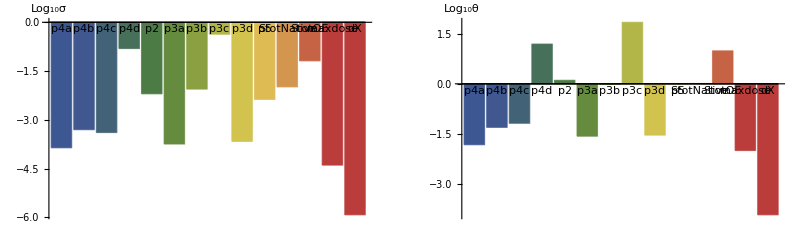

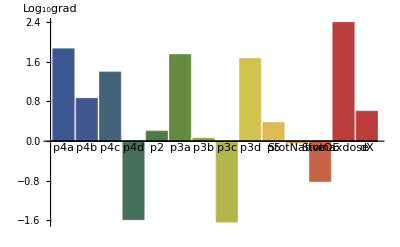

```mathematica
δL=10^-2;
σ0=δL/Abs@grad;
σ0=σ0/.ComplexInfinity->100;
σ0=MapThread[Function[{p,s},Clip[s,{0.,δp*p}]],{θ0,σ0}];
GraphicsRow[{
BarChart[Log[10,σ0],ChartLabels->v,ChartStyle->"DarkRainbow",AxesLabel->{"","Log_10σ"}],
BarChart[Log[10,θ0],ChartLabels->v,ChartStyle->"DarkRainbow",AxesLabel->{"","Log_10θ"}]},ImageSize->Full]
BarChart[Log[10,Abs@grad],ChartLabels->v,ChartStyle->"DarkRainbow",AxesLabel->{"","Log_10grad"},ImageSize->Full]
```

```mathematica
σ1=10^N@Floor@Log[10,σ0];
TableForm[{σ0,σ1}]
```

0.000137329 | 0.000495604 | 0.000404553 | 0.155556 | 0.00629666 | 0.000179294 | 0.00878264 | 0.429025 | 0.000215887 | 0.00422423 | 0.0102665 | 0.0650013 | 0.0000402536 | 1.18972×10^-6
0.0001 | 0.0001 | 0.0001 | 0.1 | 0.001 | 0.0001 | 0.001 | 0.1 | 0.0001 | 0.001 | 0.01 | 0.01 | 0.00001 | 1.×10^-6

```mathematica
TableForm[{θ0,δp θ0,σ0,σ1,grad}//SetPrecision[#,2]&,TableHeadings->{{"θ0","δp.θ0","σ0","σ1","grad"},v}]
```

| p4a | p4b | p4c | p4d | p2 | p3a | p3b | p3c | p3d | p5 | StotNative | StotOE | maxdose | dX
θ0 | 0.015 | 0.05 | 0.066 | 16. | 1.3 | 0.027 | 0.96 | 70. | 0.029 | 1. | 1. | 9.7 | 0.01 | 0.00012
δp.θ0 | 0.00015 | 0.0005 | 0.00066 | 0.16 | 0.013 | 0.00027 | 0.0096 | 0.7 | 0.00029 | 0.01 | 0.01 | 0.097 | 0.0001 | 1.2×10^-6
σ0 | 0.00014 | 0.0005 | 0.0004 | 0.16 | 0.0063 | 0.00018 | 0.0088 | 0.43 | 0.00022 | 0.0042 | 0.01 | 0.065 | 0.00004 | 1.2×10^-6
σ1 | 0.0001 | 0.0001 | 0.0001 | 0.1 | 0.001 | 0.0001 | 0.001 | 0.1 | 0.0001 | 0.001 | 0.01 | 0.01 | 0.00001 | 1.×10^-6
grad | 73. | 7.3 | 25. | 0.026 | -1.6 | -56. | -1.1 | 0.023 | -46. | 2.4 | 0.92 | 0.15 | 250. | 4.

### Viz

```mathematica
viz:=Dynamic[
GraphicsGrid[{
{ListLogPlot[{runsim$maxiter,dd}/.dat,PlotLabel->"tol"],
Plot[p3[0]/.p3sigmoid/.Smem[0][t]->Smem//.dat[[1,1]],{Smem,0,Max[Smem[0]/.dat]},PlotRange->{p3b/.dat[[1,1]],0},AxesLabel->{"Smem","p3[Smem]"}],
Plot[p4[0]/.p4sigmoid/.-Stot+Scyto[0][t]+Smem[0][t]->-Sves//.dat[[1,1]],{Sves,0,Max[Stot-Smem[0]-Scyto[0]/.dat]},PlotRange->{0,Max[{p4b,p4d}//.pθ0]},AxesLabel->{"Sves","p4[Sves]"}]
},{
ListLinePlot[{λ,Scyto[0]}/.dat,PlotLabel->"Scyto"],
ListLinePlot[{λ,Smem[0]}/.dat,PlotLabel->"Smem"],
ListLinePlot[{λ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"]
},{
ListLinePlot[{(Stot-Smem[0]-Scyto[0]),MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp vs Sves",PlotStyle->{{Dotted,Thickness[0.01]},Thick},PlotRange->{0,1},AxesLabel->{"Sves","MAPKpp"}],
ListLinePlot[{λ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp",PlotRange->{0,1}],
Show[ListPlot[{λ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat,PlotRange->5*10^0{-1,1},AxesLabel->{"Dose","MI"}],
Plot[{equNative,equOE},{x,0,1}]
]
}},ImageSize->Full]
,TrackedSymbols:>{dat}]
```

```mathematica
vizLossInput:=Table[With[{i=i},
{i,
InputField[Dynamic[w[[i]]],Number,FieldSize->{12,1}],
Dynamic[ScientificForm@SetPrecision[lossfuncsval[[i]],3]],
Dynamic[lossfuncsval[[i]]w[[i]]],
lossfuncsexp[[i]]
}],{i,1,Length[w]}]//TableForm[#,TableHeadings->{None,{"i","w","val","w.v","exp"}}]&
vizLossBar:=Dynamic[BarChart[w lossfuncsval//Reverse,BarOrigin->Left,ChartLabels->Reverse@lossfuncsexp,PlotRange->{{-0.51,2},All},AspectRatio->0.3,ImageSize->Full]]
```

### Run

```mathematica
vizLossInput
```

i | w | val | w.v | exp
1 |  |  |  | StotNative^2/.pθ
2 |  |  |  | (StotOE/StotNative-9)^2/.pθ
3 |  |  |  | (Mean[MAPKppNative]-2. Mean[MAPKppOE])^2
4 |  |  |  | Mean[SvesNative]^2
5 |  |  |  | MIerrorNative
6 |  |  |  | MIerrorOE
7 |  |  |  | equNative/.a_+b_ x→(a-2)^2
8 |  |  |  | equNative/.a_+b_ x→b^2
9 |  |  |  | (x-0.8)^2/.Solve[equOE==equNative]⟦1⟧
10 |  |  |  | (x-0.2)^2/.Solve[equOE==0]⟦1⟧

```mathematica
SPSAMaxEvals[1000]
RandomSearchInit[Loss,ToString/@v,θ0,σ1]
```

Start | Stop | Update | 
 | θk | σk | σmask
p4a |  |  | 
p4b |  |  | 
p4c |  |  | 
p4d |  |  | 
p2 |  |  | 
p3a |  |  | 
p3b |  |  | 
p3c |  |  | 
p3d |  |  | 
p5 |  |  | 
StotNative |  |  | 
StotOE |  |  | 
maxdose |  |  | 
dX |  |  |  |  |  |

```mathematica
{sol,Lhist}=SPSAGetHistory[];
θ0=Lhist[[-1,2]]
DistributeDefinitions[θ0]
```

{0.0100908,1.0001,0.0660052,8.00079,1.25055,1.99623,0.998376,0.999789,0.0503687,0.998638,1.09799,908.45,0.0100075,0.000100442}

{}

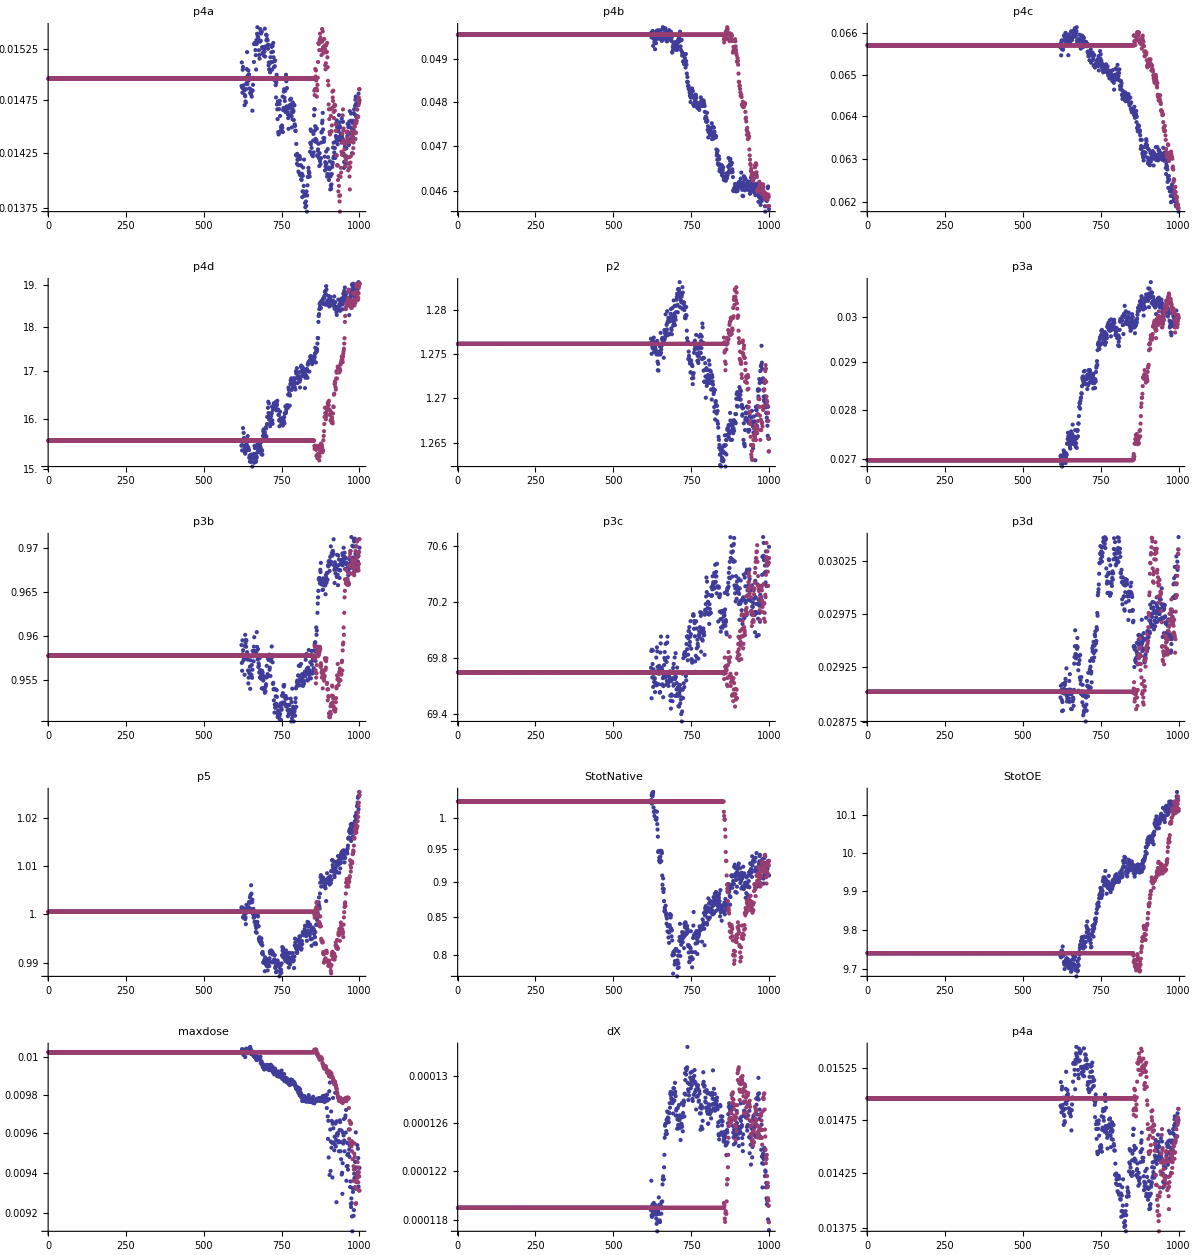

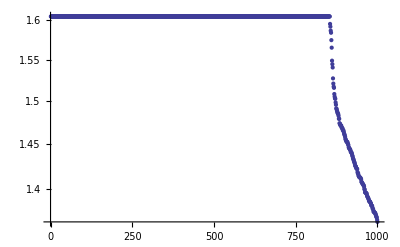

```mathematica
{sol,Lhist}=SPSAGetHistory[];
GraphicsGrid[MapThread[Function[{v,p,p2},ListLogPlot[{p,p2},PlotLabel->ToString[v],PlotRange->All]],{v,sol[[All,2]]ᵀ,Lhist[[All,2]]ᵀ}]//Partition[#,3,3,1]&,ImageSize->Full]
ListLogPlot[Lhist[[All,1]],PlotRange->All]
```

```mathematica
Dynamic[{MIerrorNative,MIerrorOE,equNative,StotNative,StotOE,Mean[SvesNative]}/.dat[[1,1]]]
```